EYP data has the peculiarity that all cells are induced, but not necessarily with the same efficiency. Therefore, we have to condition the probabilities on seeing clones of size >1.

Initial conditions

```mathematica
P0[1,0,0]:=1
P0[m_,n_,l_]:=0
```

Coupled differential equations

```mathematica
P[m_,n_,l_,t_]:=If[m<0||n<0||l<0,0,Exp[-(λ m+n γ) t] (P0[m,n,l]+∫_0^t Exp[(λ m+n γ) τ] (λ (r (m-1) P[m-1,n,l,τ]+r (m+1) P[m+1,n-2,l,τ]+(1-2 r) m P[m,n-1,l,τ])+γ (n+1) P[m,n+1,l-1,τ])ⅆτ)]
```

Combine basal cells

```mathematica
Pmn[mn_,l_,t_]:= Sum[P[m,mn-m,l,t],{m,0,mn}]
```

```mathematica
P[0,0,2,t]
P[0,1,1,t]
```

(r ((2-2 ⅇ^(-t λ)) γ^2+(-3-ⅇ^(-2 t γ)+4 ⅇ^(-t γ)) γ λ+ⅇ^(-2 t γ) (-1+ⅇ^(t γ))^2 λ^2))/(2 γ^2-3 γ λ+λ^2)

(2 ⅇ^(-2 t γ) r λ ((1-2 ⅇ^(t γ)+ⅇ^(2 t γ-t λ)) γ+(-1+ⅇ^(t γ)) λ))/(2 γ^2-3 γ λ+λ^2)

```mathematica
Cond=1-(Pmn[1,0,t]+Pmn[0,1,t]);
PDX[{{b_,s_},n_}]:=(Pmn[b,s,t]/Cond)^n
PDXT[{b_,s_}]:=Tooltip[Pmn[b,s,t]/Cond,{b,s}]
```

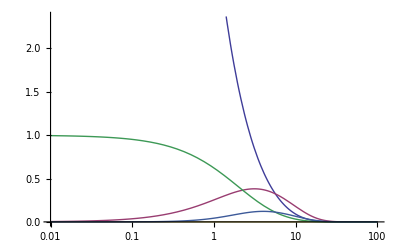

```mathematica
LogLinearPlot[Evaluate[PDXT/@{{1,0},{1,1}, {0,1}, {2,0},{2,1}} /. {λ->1/4, γ->3/4, r->0.05}], {t,0.01,100}]
```

```mathematica
Prior=PDF[UniformDistribution[{1/10,9/10}],ρ]PDF[UniformDistribution[{1/100,1/2}],r];
```

```mathematica
TotalPDX=Times@@PDX/@{{{2,0},11},{{3,0},1},{{4,0},1}, {{1,1},4},{{2,1},3},{{0,2},6}, {{0,3},1}}//.{γ->(λ ρ)/(1-ρ),t->3,λ->1/4};
```

```mathematica
{Z,Subscript[ρ, 0],Subscript[r, 0]}=NIntegrate[{1,ρ,r}*TotalPDX * Prior,{ρ,0.1,0.9},{r,0.01,0.5}];
{Subscript[ρ, 0],Subscript[r, 0]}/Z
```

{0.754307,0.365539}

```mathematica
FindMaximum[TotalPDX / Z * Prior, {ρ,0.1,0.9}, {r,0.01,0.5}]
```

{33.8749,{ρ→0.769226,r→0.38344}}

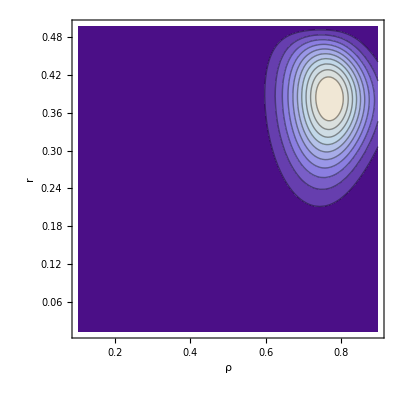

```mathematica
ContourPlot[TotalPDX / Z * Prior,{ρ,0.1,0.9}, {r,0.01,0.5},Contours->10,FrameLabel->{ρ,r}, PlotRange->All]
```